```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample/EXTRA_UPSAMPLE"];
meamFiles5={"TI_EpotminusEperf_all2_EXTRA_5_3200","TI_EpotminusEperf_all_EXTRA_5_3200"};
dftUPFiles5={"TI_UP_E0all_EXTRA_5_3200","TI_UP_Fall_EXTRA_5_3200"};
meamData5=Table[ReadList[meamFiles5[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,2}];
dftUPData5=Table[ReadList[dftUPFiles5[[i]],{Number}],{i,1,2}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols=N[{4.685,4.730,4.759,4.801,4.850},3];
eVcel2meVatom=1000/64;
```

```mathematica
Length[meamData5[[2]]]/5
dft5[[1]]//Length
```

101

100

```mathematica
Transpose[meamData5[[2]]][[5]]//Length
```

505

```mathematica
meam5=Partition[Transpose[meamData5[[2]]][[5]],Length[meamData5[[2]]]/5];
dft5=eVcel2meVatom*Table[Partition[Transpose[dftUPData5[[1]]][[1]],Length[meamData5[[2]]]/5][[i]]-Partition[Transpose[dftUPData5[[1]]][[1]],Length[meamData5[[2]]]/5][[i]][[1]],{i,1,5}];
dftf5=eVcel2meVatom*Table[Partition[Transpose[dftUPData5[[2]]][[1]],Length[meamData5[[2]]]/5][[i]]-Partition[Transpose[dftUPData5[[2]]][[1]],Length[meamData5[[2]]]/5][[i]][[1]],{i,1,5}];
```

```mathematica
(*Energy MVT TI UP-sample*)
GraphicsGrid[{{ListLinePlot[Table[(dft5-meam5)[[i]],{i,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample (meV/atom)"},ImageSize->600],ListPlot[Table[Table[Mean[(dft5-meam5)[[j]][[1;;i]]],{i,1,Length[meamData5[[2]]]/5}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample mean\n (meV/atom)"},ImageSize->600],ListPlot[Table[Table[StandardDeviation[(dft5-meam5)[[j]][[1;;i]]/Sqrt[i]],{i,2,Length[meamData5[[2]]]/5}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\n UP-samples","UP-sample uncertainty\n (meV/atom)"},PlotRange->All,ImageSize->600]}},ImageSize->2050]
Table[{Mean[(dft5-meam5)[[i]]],StandardDeviation[(dft5-meam5)[[i]]],StandardDeviation[(dft5-meam5)[[i]]]/Sqrt[Length[(dft5-meam5)[[i]]]]},{i,1,5}]//TableForm
```

-Graphics-

15.1432 | 4.44509 | 0.442303
7.88656 | 4.4569 | 0.443479
2.65205 | 3.63557 | 0.361753
-1.45456 | 3.5002 | 0.348283
-5.38734 | 4.73501 | 0.471151

```mathematica
edist5=Table[EstimatedDistribution[(dft5-meam5)[[i]],SkewNormalDistribution[μ,σ,alpha]],{i,1,5}];
edist5//TableForm
Table[EstimatedDistribution[(dft5-meam5)[[i]],NormalDistribution[μ,σ]],{i,1,5}]//TableForm
```

SkewNormalDistribution[11.3884,5.80183,1.41776]
SkewNormalDistribution[5.43448,5.06755,0.764063]
SkewNormalDistribution[0.279493,4.32614,0.944718]
SkewNormalDistribution[0.54847,4.01774,-0.799957]
SkewNormalDistribution[-2.14293,5.72053,-1.01068]

NormalDistribution[15.1432,4.42303]
NormalDistribution[7.88656,4.43479]
NormalDistribution[2.65205,3.61753]
NormalDistribution[-1.45456,3.48283]
NormalDistribution[-5.38734,4.71151]

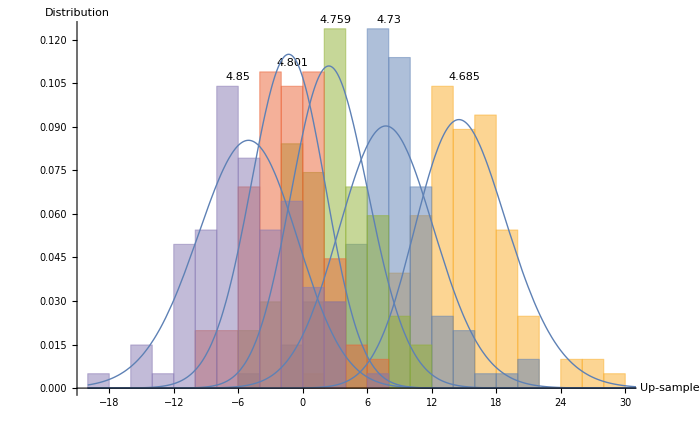

```mathematica
ldata5=Table[Labeled[(dft5-meam5)[[i]],vols[[i]],Above],{i,1,5}];
Show[Histogram[ldata5,20,"PDF",AxesLabel->{"Up-sample","Distribution"}],Plot[Table[PDF[edist5[[i]],x],{i,1,5}],{x,-20,35},PlotStyle->Thick],ImageSize->700]
```

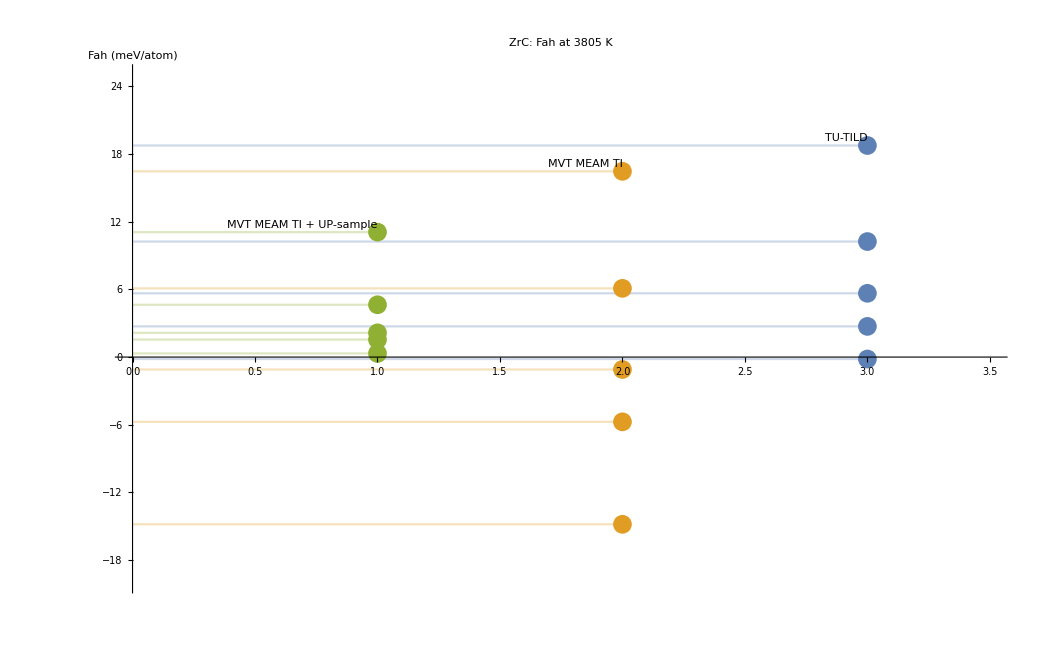

```mathematica
horizontalListPlotFill@ListPlot[{Labeled[Transpose@{Table[3,{i,1,5}],Transpose[andyFah][[4]]},"TU-TILD",Above],Labeled[Transpose@{Table[2,{i,1,5}],Transpose[MVTintAll][[4]]},"MVT MEAM TI",Above],Labeled[Transpose@{Table[1,{i,1,5}],Transpose[MVTintAll][[4]]+Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]},"MVT MEAM TI + UP-sample",Above]},PlotLegends->SwatchLegend["TU-TILD","MVT MEAM TI","MVT MEAM TI + UPsample"],PlotRange->{{0,3.5},{-20,25}},PlotLabel->"ZrC: Fah at 3805 K",AxesLabel->{"","Fah (meV/atom)"},Ticks->{None,Automatic}]
```

```mathematica
Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]
Table[Mean[(dftf5-meam5)[[i]]],{i,1,5}]
Transpose[MVTintAll][[4]]+Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]
```

{15.1432,7.88656,2.65205,-1.45456,-5.38734}

{8.4332,1.16119,-4.17762,-8.69369,-12.8361}

{0.323173,2.14656,1.55205,4.63544,11.0727}